## Solar Neutrino Flux

```mathematica
SetDirectory[NotebookDirectory[]];
```

All normalizations taken from https://arxiv.org/pdf/1104.1639.pdf

All imported flux shapes are normalized to one.

```mathematica
pp=({#⟦1⟧,6.03 10^10#⟦2⟧}&)/@Import["SolarNuFlux/pp.dat"];
n13=({#⟦1⟧,2.17 10^8#⟦2⟧}&)/@Import["SolarNuFlux/n13.dat"];
o15=({#⟦1⟧,1.56 10^8#⟦2⟧}&)/@Import["SolarNuFlux/o15.dat"];
f17=({#⟦1⟧,3.4 10^6#⟦2⟧}&)/@Import["SolarNuFlux/f17.dat"];
b8=({#⟦1⟧,4.59 10^6#⟦2⟧}&)/@Import["SolarNuFlux/b8.dat"];
hep=({#⟦1⟧,8.31 10^3#⟦2⟧}&)/@Import["SolarNuFlux/hep.dat"];
be7gs=({10^-3#⟦1⟧+0.8613,4.56 10^9#⟦2⟧}&)/@Import["SolarNuFlux/7be-gs.dat"];
be7ex=({10^-3#⟦1⟧+0.3843,4 10^8#⟦2⟧}&)/@Import["SolarNuFlux/7be-ex.dat"];
```

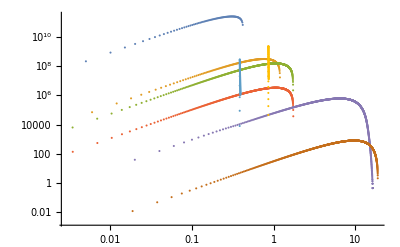

```mathematica
ListLogLogPlot[{pp,n13,o15,f17,b8,hep,be7ex,be7gs}]
```

```mathematica
MyDelta[x_,σ_]:= 1/(√(2π σ^2))Exp[-1/2 x^2/σ^2];
CutOff[x_,y_]:=UnitStep[y-x];interp=(  Interpolation[#,InterpolationOrder->1][Eν]CutOff[Eν,Last[#]⟦1⟧] &);
```

```mathematica
ppx =interp @ pp;
n13x =interp @ n13;
o15x= interp @ o15;
f17x=interp @ f17;
b8x=interp@ b8;
hepx=interp @ hep;
be7gsx=4.56 10^9 MyDelta[Eν-0.8613,0.01];
be7exx=4 10^8 MyDelta[Eν-0.3843,0.01];
pepx=1.5 10^8 MyDelta[Eν-1.44,0.01];
```

```mathematica
SolarNuOfx=ppx+n13x+o15x+f17x+b8x+hepx+be7gsx+pepx;
```

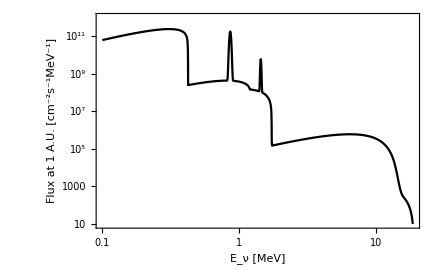

```mathematica
LogLogPlot[{SolarNuOfx},{Eν,0.1,20},PlotRange->{Automatic,{10,10^12}},Frame-> True,PlotTheme->"Monochrome",FrameLabel->(Style[#,14]&)/@{"E_ν [MeV]","Flux at 1 A.U. [cm^-2s^-1MeV^-1]"}]//Quiet
```

## Adding Oscillations (muon ONLY for now)

```mathematica
Mean[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pem.dat"]+({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pee.dat"]+({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pet.dat"]];
```

```mathematica
μFrac=Interpolation[({10^-6#⟦1⟧,#⟦2⟧}&)/@Import["SurvivalProbabilities/Pem.dat"]][Eν];
```

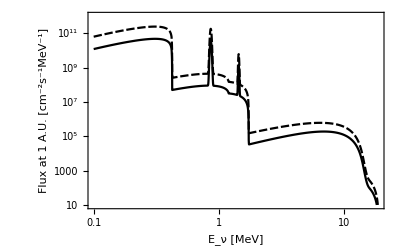

```mathematica
LogLogPlot[{μFrac SolarNuOfx,SolarNuOfx},{Eν,0.1,20},PlotRange->{Automatic,{10,10^12}},Frame-> True,PlotTheme->"Monochrome",FrameLabel->(Style[#,14]&)/@{"E_ν [MeV]","Flux at 1 A.U. [cm^-2s^-1MeV^-1]"}]//Quiet
```

## Neutrino Spectrum after scattering

```mathematica
NIntegrate[μFrac SolarNuOfx,{Eν,0,20},Method->{"DoubleExponential","SymbolicProcessing"-> 0},AccuracyGoal->Infinity]//Quiet
NIntegrate[μFrac SolarNuOfx,{Eν,0,20},Method->{"Trapezoidal","SymbolicProcessing"-> 0},AccuracyGoal->Infinity]//Quiet
```

1.26942×10^10

1.26938×10^10

```mathematica
NormSolarNuOfx=1/(1.2693788196538383*10^10)SolarNuOfx;
```

```mathematica
σ=-(α d^2 mN^4 Z^2)/(Eν^2 tMax)+(α d^2 mN^4 Z^2)/(Eν^2 tMin)-(α d^2 mN^2 Z^2 Log[tMax/tMin])/Eν^2+4 α d^2 Z^2 Log[(tMax/tMin)];
σRed=-σ/(α d^2 Z^2)/. {tMax-> -Eν(Eν-√(Eν^2-mN^2)),tMin->- (2 Eν^2-mN^2)}//Simplify (* Red is for reduced*)
```

mN^4 (1/(2 Eν^4-Eν^2 mN^2)-1/(Eν^3 (Eν-√(Eν^2-mN^2))))+(-4+mN^2/Eν^2) Log[(Eν (Eν-√(Eν^2-mN^2)))/(2 Eν^2-mN^2)]

```mathematica
fluxHNL=μFrac NormSolarNuOfx σRed;
```

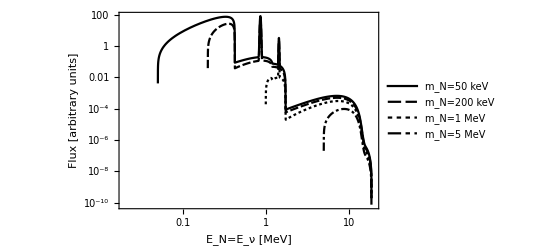

```mathematica
LogLogPlot[{fluxHNL/.mN-> 0.05,fluxHNL/.mN-> 0.2,fluxHNL/.mN-> 1,fluxHNL/.mN-> 5},{Eν,0,20},Frame-> True, PlotTheme->"Monochrome",PlotLegends->Placed[{"m_N=50   keV","m_N=200 keV","m_N=1     MeV","m_N=5     MeV"},{0.22,0.3}],FrameLabel->(Style[#,12]&)/@{"E_N=E_ν  [MeV]","Flux   [arbitrary units]"},FrameTicks->{Automatic,Automatic}]//Quiet
```

```mathematica
Export["fluxHNL.m",fluxHNL]
```

fluxHNL.m

## Photon Distribution from dz “slab”

## ζ =0

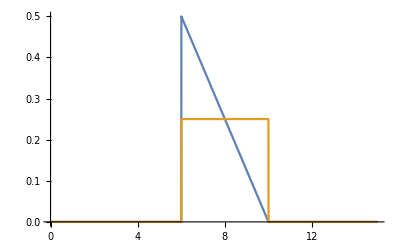

```mathematica
sawTooth=2(EγMax-Eγ)/(EγMax-EγMin)^2 UnitStep[EγMax-Eγ,Eγ-EγMin];
box=1/(EγMax-EγMin)UnitStep[EγMax-Eγ,Eγ-EγMin];
Plot[{sawTooth/.{EγMax->  10,EγMin->  6},box/.{EγMax->  10,EγMin->  6}},{Eγ,0,15}]
boxIntegrandGG=10/Eν √(0.99/(1-mN^2/Eν^2)) fluxHNL  box /. {EγMin->Eν/2(1-√(1-mN^2/Eν^2)) , EγMax->Eν/2(1+√(1-mN^2/Eν^2)) };
sawIntegrandGG=10/Eν √(0.99/(1-mN^2/Eν^2)) fluxHNL  sawTooth /. {EγMin->Eν/2(1-√(1-mN^2/Eν^2)) , EγMax->Eν/2(1+√(1-mN^2/Eν^2)) };
```

```mathematica
(*Check that they are actually different*)
```

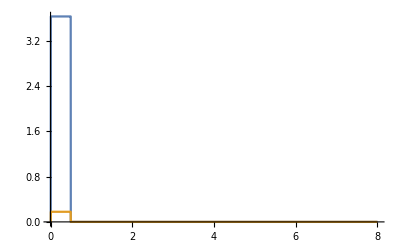

```mathematica
Plot[{boxIntegrandGG/.{Eν-> 0.5,mN-> 0.1},boxIntegrandLL/.{Eν-> 0.5,mN-> 0.1}},{Eγ,0,8}]//Quiet
```

```mathematica
makeBoxSpectrumGG[mNN_]:=Block[{mN},Return[Table[
{Eγ,NIntegrate[boxIntegrandGG/.mN-> mNN,{Eν,mNN,18.8},Method->{Automatic,"SymbolicProcessing"-> 0},AccuracyGoal-> 10]},{Eγ,Table[0.001 1.1^n,{n,0,(log(20/0.001))/(log(1.1))+1}]}]//Quiet]];
makeSawSpectrumGG[mNN_]:=Block[{mN},Return[Table[
{Eγ,NIntegrate[sawIntegrandGG/.mN-> mNN,{Eν,mNN,18.8},Method->{Automatic,"SymbolicProcessing"-> 0},AccuracyGoal-> 10]},{Eγ,Table[0.001 1.1^n,{n,0,(log(20/0.001))/(log(1.1))+1}]}]//Quiet]];
```

```mathematica
sawSpecDictGG=<||>;
Do[sawSpecDictGG[mN]=makeSawSpectrumGG[mN],{mN,Table[0.01 1.25^n,{n,0,34}]}];
```

```mathematica
boxSpecDictGG=<||>;
Do[boxSpecDictGG[mN]=makeBoxSpectrumGG[mN],{mN,Table[0.01 1.25^n,{n,0,34}]}];
```

```mathematica
Export["N-Specs/sawSpecsGG.m",sawSpecDictGG];
Export["N-Specs/boxSpecsGG.m",boxSpecDictGG];
```

## ζ=∞

```mathematica
sawTooth=2(EγMax-Eγ)/(EγMax-EγMin)^2 UnitStep[EγMax-Eγ,Eγ-EγMin];
box=1/(EγMax-EγMin)UnitStep[EγMax-Eγ,Eγ-EγMin];
Plot[{sawTooth/.{EγMax->  10,EγMin->  6},box/.{EγMax->  10,EγMin->  6}},{Eγ,0,15}]
boxIntegrandLL=fluxHNL  box /. {EγMin->Eν/2(1-√(1-mN^2/Eν^2)) , EγMax->Eν/2(1+√(1-mN^2/Eν^2)) };
sawIntegrandLL=fluxHNL  sawTooth /. {EγMin->Eν/2(1-√(1-mN^2/Eν^2)) , EγMax->Eν/2(1+√(1-mN^2/Eν^2)) };
```

-Graphics-

```mathematica
makeBoxSpectrumLL[mNN_]:=Block[{mN},Return[Table[
{Eγ,NIntegrate[boxIntegrandLL/.mN-> mNN,{Eν,mNN,18.8},Method->{Automatic,"SymbolicProcessing"-> 0},AccuracyGoal-> 10]},{Eγ,Table[0.001 1.1^n,{n,0,(log(20/0.001))/(log(1.1))+1}]}]//Quiet]];
makeSawSpectrumLL[mNN_]:=Block[{mN},Return[Table[
{Eγ,NIntegrate[sawIntegrandLL/.mN-> mNN,{Eν,mNN,18.8},Method->{Automatic,"SymbolicProcessing"-> 0},AccuracyGoal-> 10]},{Eγ,Table[0.001 1.1^n,{n,0,(log(20/0.001))/(log(1.1))+1}]}]//Quiet]];
```

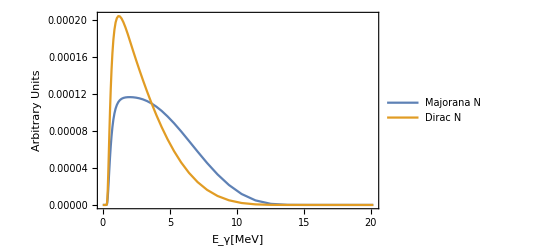

```mathematica
ListPlot[{makeBoxSpectrumLL[4],makeSawSpectrumLL[4]},Joined->True,PlotLegends->Placed[{"Majorana N","Dirac N"},{0.6,0.7}],Frame->True,FrameStyle->Black,FrameLabel->{"E_γ[MeV]","Arbitrary Units", "Spectral Shape of Photons from ν → N → ν γ "},PlotRange->Full]
```

```mathematica
sawSpecDictLL=<||>;
Do[sawSpecDictLL[mN]=makeSawSpectrumLL[mN],{mN,Table[0.01 1.25^n,{n,0,34}]}];
```

```mathematica
boxSpecDictLL=<||>;
Do[boxSpecDictLL[mN]=makeBoxSpectrumLL[mN],{mN,Table[0.01 1.25^n,{n,0,34}]}];
```

```mathematica
Export["N-Specs/sawSpecsLL.m",sawSpecDictLL];
Export["N-Specs/boxSpecsLL.m",boxSpecDictLL];
```

## Comparison between ζ=0 and ζ=∞

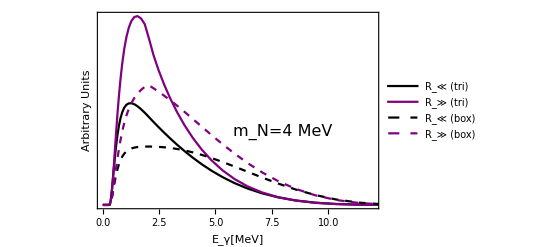

```mathematica
ListPlot[{makeSawSpectrumLL[4],makeSawSpectrumGG[4],makeBoxSpectrumLL[4],makeBoxSpectrumGG[4]},Joined->True,PlotStyle->{{Black},{Purple},{Black,Dashed},{Purple,Dashed}},PlotRange-> {{0,12},Automatic},PlotLegends->Placed[{"R_≪ (tri) ","R_≫ (tri)","R_≪ (box) ","R_≫ (box)"},{0.6,0.7}],Frame->True,FrameStyle->Black,FrameLabel->(Style[#,14]&)/@{"E_γ[MeV]","Arbitrary Units", "Spectral Shape of Photons from ν → N → ν γ "},FrameTicks->{Automatic,None},PlotRange->Full,Epilog->Inset[Style["m_N=4 MeV",16],{8,0.00009}]]
```

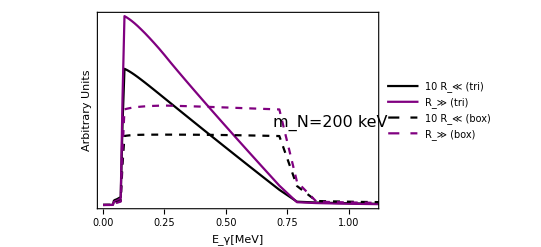

```mathematica
ListPlot[{({#⟦1⟧,10# ⟦2⟧}&)/@ makeSawSpectrumLL[0.5],makeSawSpectrumGG[0.5],({#⟦1⟧,10 #⟦2⟧}&)/@makeBoxSpectrumLL[0.5],makeBoxSpectrumGG[0.5]},Joined->True,PlotStyle->{{Black},{Purple},{Black,Dashed},{Purple,Dashed}},PlotRange-> {{0,1.1},Full},PlotLegends->Placed[{"10 R_≪ (tri) ","R_≫ (tri)","10 R_≪ (box) ","R_≫ (box)"},{0.7,0.75}],Frame->True,FrameStyle->Black,FrameLabel->(Style[#,14]&)/@{"E_γ[MeV]","Arbitrary Units", "Spectral Shape of Photons from ν → N → ν γ "},FrameTicks->{Automatic,None},Epilog->Inset[Style["m_N=200 keV",16],{0.925,10}]]
```